## Initializing the Notebook

### Set up MASS toolbox and other Packages

```mathematica
Quit[]
```

```mathematica
<<MASSToolbox`
<<MASSToolbox`Style`
Import["/media/users/jdebree/Mathematica/ToPython.m"]
iJO=Import["/media/users/dzielinski/massmodels/models/iJO1366/iJO1366.m.gz"];
```

### Set up Directories

```mathematica
workingDir = "/media/users/jdebree/Mathematica/ADK1/";
psoScriptPath="/media/users/jdebree/Mathematica/pso_short_ver0.05.py";

date=Date[];
dateString="Run_"<>ToString[date[[2]]]<>"_"<>ToString[date[[3]]]<>"_"<>ToString[date[[4]]]<>"."<>ToString[date[[5]]];

Choose One;
(*Comment and uncomment to select one 'alt'+'/'*)
(*outputDir = dateString;(*Unique*)*)
(*outputDir = "Run_Unspecified";(*Non-Unique*)*)
outputDir = "Development";(*Non-Unique*)
(*End options*)

outputPath =workingDir<>"PSO_files/"<>outputDir<>"/";
mkDirCmd = "!mkdir "<>outputPath<> " 2>&1";
Import[mkDirCmd,"Text"]
```

mkdir: cannot create directory `/media/users/jdebree/Mathematica/ADK1/PSO_files/Development/': File exists

## Running One Primary Enzyme Module

## Construct ADK1 Module and Set Up Equations (Primary)

### Construct enzyme module

```mathematica
rxn=Cases[iJO["Reactions"],r_reaction/;getID[r]==="ADK1"][[1]]

catalyticBranch={"E_ADK1[c] + amp[c] <=> E_ADK1[c]&amp",
				"E_ADK1[c] + atp[c] <=> E_ADK1[c]&atp",
				"E_ADK1[c]&atp + amp[c] <=> E_ADK1[c]&atp&amp",
				"E_ADK1[c]&amp + atp[c] <=> E_ADK1[c]&atp&amp",
				"E_ADK1[c]&atp&amp <=> E_ADK1[c]&adp&adp",
				"E_ADK1[c]&adp&adp <=> E_ADK1[c]&adp + adp[c]",
				"E_ADK1[c]&adp <=> E_ADK1[c] + adp[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
```

(amp^c+atp^c⇌2 adp^c)^ADK1

```mathematica
(*Visualize Module (Optional);*)
enzymeModel["Reactions"]
visualizePathways[enzymeModel];(*Caution: Graphics can be unstable*)
enzymeModel;
```

{((ADK1^c)_^+atp^c⇌(ADK1^c&atp^c)_^)^ADK11,((ADK1^c)_^+amp^c⇌(ADK1^c&amp^c)_^)^ADK12,((ADK1^c&adp^c)_^⇌(ADK1^c)_^+adp^c)^ADK13,((ADK1^c&amp^c)_^+atp^c⇌(ADK1^c&atp^c&amp^c)_^)^ADK14,((ADK1^c&atp^c)_^+amp^c⇌(ADK1^c&atp^c&amp^c)_^)^ADK15,((ADK1^c&adp^c&adp^c)_^⇌(ADK1^c&adp^c)_^+adp^c)^ADK16,((ADK1^c&atp^c&amp^c)_^⇌(ADK1^c&adp^c&adp^c)_^)^ADK17}

### Setup King-Altmann Equations

```mathematica
reverseZeroSub={m["adp","c"]->0};
forwardZeroSub={m["amp","c"]->0,m["atp","c"]->0};
metSatForSub={m["amp","c"]->∞,m["atp","c"]->∞};
metSatRevSub={m["adp","c"]->∞};
volumeSub={parameter["Volume","c"]->1};
KeqName="ADK1";
KeqVal=2.3;
```

```mathematica
transitionIndex={};
forwardBindingIndex={};
reverseBindingIndex={};
allReactions=enzymeModel["Reactions"];(*ADD A PARSE FOR ONLY CATALYTIC REACTIONS*)
sumReactionStoich=Table[Total[getSignedStoich[allReactions[[eqn]]]],{eqn,Length[allReactions]}];
Do[If[sumReactionStoich[[eqn]] ==0,transitionIndex=Append[transitionIndex,eqn]],{eqn,Length[sumReactionStoich]}];(*Extract the transition step(s)*)
Do[If[sumReactionStoich[[eqn]] <0,forwardBindingIndex=Append[forwardBindingIndex,eqn]],{eqn,Length[sumReactionStoich]}];(*Extract the binding step(s) if the reaction is proceeding forward*)
Do[If[sumReactionStoich[[eqn]] >0,reverseBindingIndex=Append[reverseBindingIndex,eqn]],{eqn,Length[sumReactionStoich]}];(*Extract the binding step(s) if the reaction is proceeding in reverse*)

kaPatterns=unifyRateConstants[keq2k[KingAltmanPatterns[enzymeModel]]];
kaPatterns=anonymize[Simplify[kaPatterns]];
allRateConsts=Union[Cases[{kaPatterns},_rateconst,∞]];
catalyticRxns=allReactions;
haldane=unifyRateConstants[haldaneRelation[KeqName,catalyticRxns]];
haldaneSubOutParameter=Table[enzymeModel["ReverseRateConstants"][[transitionIndex[[i]]]],{i,Length[transitionIndex]}];
haldaneSub=Quiet[Solve[haldane/.{haldane[[1]]->KeqVal},haldaneSubOutParameter[[1]]][[1]],{Solve::ratnz}];
rates=enzymeModel["Rates"]/.elem_[t]:>elem;

(*Each distinct substrate needs it own relative rate*)

absoluteRateForward=(Simplify[keq2k[unifyRateConstants[rates[[transitionIndex[[1]]]]]]/.kaPatterns]/.reverseZeroSub/.volumeSub)/.haldaneSub;
absoluteRateReverse=(-Simplify[keq2k[unifyRateConstants[rates[[transitionIndex[[1]]]]]]/.kaPatterns]/.forwardZeroSub/.volumeSub)/.haldaneSub;
relativeRateForward=Table[absoluteRateForward/(Limit[Simplify[keq2k[unifyRateConstants[rates[[transitionIndex[[1]]]]]]/.kaPatterns]/.reverseZeroSub/.volumeSub,metSatForSub[[i]]]/.haldaneSub),{i,1,Length[metSatForSub]}];
relativeRateReverse=Table[-absoluteRateReverse/(Limit[Simplify[keq2k[unifyRateConstants[rates[[transitionIndex[[1]]]]]]/.kaPatterns]/.forwardZeroSub/.volumeSub,metSatRevSub[[i]]]/.haldaneSub),{i,1,Length[metSatRevSub]}];

finalRateConsts=Variables[Union[Cases[Flatten[Join[{absoluteRateForward},{absoluteRateReverse},relativeRateForward,relativeRateReverse]],_rateconst|_Keq,∞]]];
rateConstsSub=Thread[finalRateConsts->Table["x["<>ToString[i]<>"]",{i,0,Length[finalRateConsts]-1}]];

finalMets=Union[Cases[Flatten[Join[{absoluteRateForward},{absoluteRateReverse},relativeRateForward,relativeRateReverse]],_metabolite|_parameter,∞]];
metsSub=Thread[finalMets->Table["d["<>ToString[i]<>"]",{i,0,Length[finalMets]-1}]];
```

### Check Equations (Optional)

```mathematica
absoluteRateForwardFinal=absoluteRateForward/.rateConstsSub/.metsSub
ToPython[absoluteRateForwardFinal]
```

### Export Equations

```mathematica
eqnNameList={"absRateFor1","absRateRev1","relRateFor1","relRateFor2","relRateRev1"};

eqnValListPy={ToPython[absoluteRateForward/.rateConstsSub/.metsSub],
			ToPython[absoluteRateReverse/.rateConstsSub/.metsSub],
			ToPython[relativeRateForward[[1]]/.rateConstsSub/.metsSub],
			ToPython[relativeRateForward[[2]]/.rateConstsSub/.metsSub],
			ToPython[relativeRateReverse[[1]]/.rateConstsSub/.metsSub]};

eqnValList={absoluteRateForward,
			absoluteRateReverse,
			relativeRateForward[[1]],
			relativeRateForward[[2]],
			relativeRateReverse[[1]]};
eqnList={eqnNameList,eqnValListPy,eqnValList};
fileList=Table[outputPath<>eqnname<>".txt",{eqnname,eqnList[[1]]}];
fileListSub=Table[fileList[[i]]->eqnValList[[i]],{i,1,Length[fileList]}];
Do[Export[fileList[[i]],eqnList[[2,i]]],{i,1,Length[eqnList[[2]]]}];
```

#### Assemble and Export Linear Constraints (*Not Fully Implemented Yet*)

```mathematica
forwardRateConsts=enzymeModel["ForwardRateConstants"];
reverseRateConsts=enzymeModel["ReverseRateConstants"];
forwardDissociationConsts=Table[forwardRateConsts[[forwardBindingIndex[[index]]]]-reverseRateConsts[[forwardBindingIndex[[index]]]],{index,Length[forwardBindingIndex]}];
reverseDissociationConsts=Table[reverseRateConsts[[reverseBindingIndex[[index]]]]-forwardRateConsts[[reverseBindingIndex[[index]]]],{index,Length[reverseBindingIndex]}];
linearConstraintsForFitting=Join[forwardDissociationConsts,reverseDissociationConsts];
linearConstraintsForFittingPy=Table[ToString[linearConstraintsForFitting[[i]]/.rateConstsSub],{i,Length[linearConstraintsForFitting]}];
Export[outputPath<>"linearConstraints.txt",linearConstraintsForFittingPy,"Table"];
```

## Simulate Data (Primary)

### Setting Parameters to Generate Data

```mathematica
extraData = {pHVal,tempVal,fileFlag};
extraDataNames={"pH","temp","fileFlag","vRel"};
totalVarListNames = Join[getID/@metsSub[[All,1]],extraDataNames];
totalVarList = Join[metsSub[[All,1]],extraData];
KmList={KmAdp,KmAtp,KmAmp,n}={0.000105,0.000046,0.000044,1};
vAbsValWeight = 10; (*Number of times a kcat value is repeated to weight it when fitting*)
fileFlagList = fileList;
```

### Generating Data and Sum of Squared Errors Equation

```mathematica
vList={};(*Data*)
sumSqrdErrorsElements = {};(*Sum of Squared Errors*)
ADP  (All concentrations in Mol/L);
extraSub = {pHVal-> 7.4,tempVal-> 40,fileFlag-> fileFlagList[[5]]};
metsSubData = {m["amp","c"]-> 0,m["atp","c"]-> 0,parameter["Etot"]-> 1};
varMet = m["adp","c"];
kmData = KmAdp;
varMetIndex = 1;

{minRange, maxRange,step}={(Log10[kmData]-1),(Log10[kmData]+1),.2};
dataRange = Table[totalVarList/.extraSub/.metsSubData/.varMet->10^i,{i,minRange,maxRange,step}];

vRelVal= #^n/(kmData^n+#^n)&/@dataRange[[All,varMetIndex]];
vList = Append[vList, Table[Join[dataRange[[i]],{vRelVal[[i]]}],{i,1,Length[dataRange]}]];

dataSub = Table[Thread[metsSub[[All,1]]->dataRange[[All,1;;4]][[i]]],{i,1,Length[dataRange]}];

dataSubbedEqn=Table[extraSub[[All,2]][[3]]/.fileListSub/.dataSub[[i]],{i,1, Length[dataSub]}];
sqrdErrorsEqn = Table[(dataSubbedEqn[[i]]-vRelVal[[i]])^2,{i,1,Length[dataSubbedEqn]}];
sumSqrdErrorsElements=Append[sumSqrdErrorsElements,Total[sqrdErrorsEqn]];

ATP  (All concentrations in Mol/L);
extraSub = {pHVal-> 7.4,tempVal-> 40,fileFlag-> fileFlagList[[4]]};
metsSubData = {m["amp","c"]-> 0.001,m["adp","c"]-> 0,parameter["Etot"]-> 1};
varMet = m["atp","c"];
kmData = KmAtp;
varMetIndex = 3;

{minRange, maxRange,step}={(Log10[kmData]-1),(Log10[kmData]+1),.2};
dataRange = Table[totalVarList/.extraSub/.metsSubData/.varMet->10^i,{i,minRange,maxRange,step}];

vRelVal= #^n/(kmData^n+#^n)&/@dataRange[[All,varMetIndex]];
vList = Append[vList,Table[Join[dataRange[[i]],{vRelVal[[i]]}],{i,1,Length[dataRange]}]];

dataSub = Table[Thread[metsSub[[All,1]]->dataRange[[All,1;;4]][[i]]],{i,1,Length[dataRange]}];
dataSubbedEqn=Table[extraSub[[All,2]][[3]]/.fileListSub/.dataSub[[i]],{i,1, Length[dataSub]}];
sqrdErrorsEqn = Table[(dataSubbedEqn[[i]]-vRelVal[[i]])^2,{i,1,Length[dataSubbedEqn]}];
sumSqrdErrorsElements=Append[sumSqrdErrorsElements,Total[sqrdErrorsEqn]];

AMP  (All concentrations in Mol/L);
extraSub = {pHVal-> 7.4,tempVal-> 40,fileFlag-> fileFlagList[[3]]};
metsSubData = {m["atp","c"]-> 0.001,m["adp","c"]-> 0,parameter["Etot"]-> 1};
varMet = m["amp","c"];
kmData = KmAmp;
varMetIndex = 2;

{minRange, maxRange,step}={(Log10[kmData]-1),(Log10[kmData]+1),.2};
dataRange = Table[totalVarList/.extraSub/.metsSubData/.varMet->10^i,{i,minRange,maxRange,step}];

vRelVal= #^n/(kmData^n+#^n)&/@dataRange[[All,varMetIndex]];
vList = Append[vList,Table[Join[dataRange[[i]],{vRelVal[[i]]}],{i,1,Length[dataRange]}]];

dataSub = Table[Thread[metsSub[[All,1]]->dataRange[[All,1;;4]][[i]]],{i,1,Length[dataRange]}];

dataSubbedEqn=Table[extraSub[[All,2]][[3]]/.fileListSub/.dataSub[[i]],{i,1, Length[dataSub]}];
sqrdErrorsEqn = Table[(dataSubbedEqn[[i]]-vRelVal[[i]])^2,{i,1,Length[dataSubbedEqn]}];
sumSqrdErrorsElements=Append[sumSqrdErrorsElements,Total[sqrdErrorsEqn]];

kcat[ADP] value (All concentrations in Mol/L);
extraSub = {pHVal-> 7.4,tempVal-> 40,fileFlag-> fileFlagList[[2]]};
metsSubData = {m["atp","c"]-> 0,m["amp","c"]-> 0,parameter["Etot"]-> 1};
varMet = m["adp","c"];
kcatRev=319;
kmData = KmAdp;
varMetIndex = 1;

dataPoint = totalVarList/.extraSub/.metsSubData/.varMet->0.01;
vAbsVal= #^n/(kmData^n+#^n)*kcatRev*parameter["Etot"]/.metsSubData&/@{dataPoint[[varMetIndex]]};

vList =Append[vList,Table[Join[dataPoint,vAbsVal],{i,1,vAbsValWeight}]];

dataSub = Table[Thread[metsSub[[All,1]]->dataPoint[[1;;4]]],{i,1,vAbsValWeight}];
dataSubbedEqn=extraSub[[All,2]][[3]]/.fileListSub/.dataSub;

vRelVal = Table[vAbsVal[[1]],{i,1,vAbsValWeight}];(*Weighting repetition factor*)

sqrdErrorsEqn = Table[(dataSubbedEqn[[i]]-vRelVal[[i]])^2,{i,1,Length[vRelVal]}];
sumSqrdErrorsElements=Append[sumSqrdErrorsElements,Total[sqrdErrorsEqn]];

kcat[ATP,AMP] value (All concentrations in Mol/L);
extraSub = {pHVal-> 7.4,tempVal-> 40,fileFlag-> fileFlagList[[1]]};
metsSubData = {m["adp","c"]-> 0,parameter["Etot"]-> 1};
varMet = {m["amp","c"]-> 0.01,m["atp","c"]->0.01};
kcatFor =1296;
kmData = {KmAmp,KmAtp};
dataPoint = {totalVarList/.extraSub/.metsSubData/.varMet};

vAbsVal= (#1[[3]] #1[[2]])^n/((kmData[[1]] #1[[3]])^n+(kmData[[2]] #1[[2]])^n+(#1[[3]] #1[[2]])^n)*kcatFor*parameter["Etot"]/.metsSubData&/@dataPoint;


vList = Append[vList,Table[Join[Flatten[dataPoint,1],vAbsVal],{i,1,vAbsValWeight}]];


dataSub = Table[Thread[metsSub[[All,1]]->dataPoint[[1,1;;4]]],{i,1,vAbsValWeight}];
dataSubbedEqn=extraSub[[All,2]][[3]]/.fileListSub/.dataSub;

vRelVal = Table[vAbsVal[[1]],{i,1,vAbsValWeight}];(*Weighting repetition factor*)

sqrdErrorsEqn = Table[(dataSubbedEqn[[i]]-vRelVal[[i]])^2,{i,1,Length[vRelVal]}];
sumSqrdErrorsElements=Append[sumSqrdErrorsElements,Total[sqrdErrorsEqn]];


vListData = Flatten[vList,1];
sumSqrdErrorsEqn=Total[sumSqrdErrorsElements];
```

### Change pH form (Optional)

```mathematica
Thread[vListData[[All,5]]=10^(-1*vListData[[All,5]])] (*Swaps pH for [H] in mol/L*)
```

```mathematica
Thread[vListData[[All,5]]=-1*Log10[vListData[[All,5]]]] (*Swaps [H] in mol/L for pH*)
```

### Writing to a .txt file

```mathematica
dataPath =outputPath<>"ADK1.dat";
ssePath = outputPath <>"SSE.txt";

(*Data file;*)

header = {totalVarListNames};
vList=Join[header,vListData];
Export[dataPath,vList,"Table"];

(*Sum of Squared Errors Equation;*)

sumSqrdErrorsEqnPy =ToPython[sumSqrdErrorsEqn/.rateConstsSub/.metsSub];
Export[ssePath,sumSqrdErrorsEqnPy,"Table"];
```

#### Check That Files Were Exported (Optional)

```mathematica
FilePrint[dataPath](*Optional*)
```

```mathematica
FilePrint[ssePath](*Optional*)(*Kind of buggy*)
```

## Run the Particle Swarm Optimization (Primary)

### Notes:

```mathematica
(*
	There is not currently a lot of support for interfacing python inside of Mathematica. In order to accomplish this, the approach taken in this script has been to pass dependencies and results through text files. Equations are given in their raw forms, while other variables are given as a list of lists, where each sublist is one variable in the form of:
			 {"Python_Variable_Name", mathematicaAssignment = "Acutal Value"}
The list of lists is exported using the Table function to create a tab delimited .txt file. The Particle Swarm Optimization Algorithm reads the file, imports the variables as dict() object (e.g. parameter["Python_Variable_Name"] = "Acutal Value"), and reassigns the values to working variables.

Additionally, the functionality to run the PSO Algorithm directly from this notebook has been added, but ideally you should be running it in a separate shell window because of interfacing issues.
*)
```

### Setting the Python Script Parameters

#### Set Parameter reading filepath CHOOSE ONE:

```mathematica
(*Use when running the PSO algorithm Locally, on this machine*)
paramOutputPath= workingDir<>"PSO_files/"<>outputDir<>"/";
```

```mathematica
(*Use when running the PSO algorithm on another system (e.g. NERSC)*)
paramWorkingDir = "/global/homes/d/dczielin/ProjectFiles/ADK1/";
paramOutputPath= paramWorkingDir<>"PSO_files/"<>outputDir<>"/";
```

#### Write Parameters to a File

```mathematica
psoParameters={       (*Basic Options*)
				(*This section provides the necessary options for most users;*)

(*Flag for ;
input locations;*)

				(*General Python Configuration;*)

		(*These parameters determine how Python runs the PSO Algorithm;
			-Multiprocessing is a built-in python module and should be used if you are running the ;
				algorithm on a single machine (i.e. Having only one Python namespace);
				-num_Cpus -> Dependent parameter of using Multiprocessing and determines the ;
					number of processor cores utilized by the PSO Algorithm );*)

(*Inputs*)
				{"num_Cpus",numCpus =28},
(**)

				(*PSO Algorithm Behavior*)

				(*PSO Algorithm Scaling;
			-These parameters drastically effect computation time;
			-num_trial -> The number of separate PSO runs;
			-num_generations -> The maximum number of iterations taken during each PSO run;
			-val_pop_size -> number of individual particles in each PSO run (default = 20);*)

(*Inputs*)
				{"num_trial",numTrial=5},
				{"num_generations",numGenerations=100},
				{"val_pop_size",popSize=100},
				{"bestFitnessCutoff",bestFitnessCutoff=10.0},
(**)

				(*PSO Algorithm Configuration;
			-val_neigh_size -> neighborhood_size;
			-val_inertia -> inertia;
			-val_cogn_rate -> cognitive_rate;
			-val_soc_rate -> social_rate;
			-The default parameter values are:      ;
				neighborhood_size = 3;
				inertia = 1;
				social_rate = 2.1;
				cognitive_rate = 2.1;*)

(*Inputs*)
				{"val_neigh_size",neighborSize=3},
				{"val_inertia",inertia=1},
				{"val_cogn_rate",cognitiveRate=2.1},
				{"val_soc_rate",socialRate=2.1},
(**)

				(*Advanced Options*)
				(*This section provides all of the available options;*)
			
		(*General Python Algorithm Configuration;*)(*
			-Each of the following options are modifications to the original ECspy module (i.e. default = False);
			-use_Keep_Best -> Boolean switch that forces the PSO algorithm to hold onto the best candidate;
			-use_Random_Replace -> Soolean switch for randomly replacing a percentage of the swarm particles ;
				with random candidates;
			-percent_Rand -> Percentage of swarm particles replaced. Should be 0.0 > and < 1.0; *)

(*Inputs*)
				{"use_Keep_Best",useKeepBest ="True"},
				{"use_Random_Replace",useRandomReplace ="True"},
				{"percent_Rand",percentRandomParticles=0.05},
				
(**)

				(*PSO Algorithm*)

				(*Dependencies for setting boundaries for the PSO target values;
			-The bounds are in Log Space and set automatically to (-12, 2) and (-7, 9) for Kd's and Forward rate constansts, respectively ;
			-numFuncVar is set automatically;*)

(*Inputs*)            (*Fix this section*)
				{"lower_bound",lowerBounds=ToPython[Table[If[MemberQ[Cases[rateConstsSub,_Keq,∞],finalRateConsts[[variable]]],-12,-6],{variable,Length[finalRateConsts]}]]},
				{"upper_bound",upperBounds=ToPython[Table[If[MemberQ[Cases[rateConstsSub,_Keq,∞],finalRateConsts[[variable]]],2,9],{variable,Length[finalRateConsts]}]]},
				{"num_func_var",numFuncVar=Length[finalRateConsts]},
(**)

				(*File Pathways for Evaluation Equation (SSE) and Recording Files*)
				(*    -sse_name -> The filepath to the evaluation equation (SSE);
			-The files record the following information: ;
				psoStatsFileName -> Summary of each generation;
				trialSummaryFileName -> Summary of each trial;
				resultsFileName -> Final candidate values;*)

(*Inputs*)
				{"sse_name",sseEqn = paramOutputPath<>"SSE.txt"},
				{"summary_file_name",trialSummaryFileName=paramOutputPath<>"summary.txt"},
				{"ultimate_result_name",resultsFileName =paramOutputPath<>"results.txt"}
(**)

				};

parameterPath =outputPath<>"psoParameters.txt";
Export[parameterPath,psoParameters,"Table"];
```

```mathematica
(*Optional*)
FilePrint[parameterPath]
```

### Running the Script Locally Using a Shell Script

```mathematica
(*Make A Shell Script*)
shebangLine={"#!/bin/bash"};
shRunPso={shebangLine,{(*Spacer*)}};
shRunPso=Append[shRunPso,{"# Initialize Files"}];
shRunPso=Append[shRunPso,{"header=\"elapsed_time, best.fitness, num_generations, pop_size, neighborhood_size, inertia, cognitive_rate, social_rate\""}];
shRunPso=Append[shRunPso,{"echo $header > "<>trialSummaryFileName}];
shRunPso=Append[shRunPso,{"> "<>resultsFileName}];
shRunPso=Append[shRunPso,{(*Spacer*)}];
shRunPso=Append[shRunPso,{"# Import Dependencies"}];
shRunPso=Append[shRunPso,{"num_trials="<>ToString[numTrial]}];
shRunPso=Append[shRunPso,{"trial_num=1"}];
shRunPso=Append[shRunPso,{(*Spacer*)}];
shRunPso=Append[shRunPso,{"while ((trial_num<=num_trials))"}];
shRunPso=Append[shRunPso,{"do"}];
shRunPso=Append[shRunPso,{"    echo \"Trial Number: $trial_num\""}];
shRunPso=Append[shRunPso,{"    python "<>psoScriptPath<>" "<>parameterPath<>" "<>trialSummaryFileName<>" "<>resultsFileName}];
shRunPso=Append[shRunPso,{"    let trial_num+=1"}];
shRunPso=Append[shRunPso,{"done"}];

shRunPsoPath=outputPath<>"runPso.sh";
Export[shRunPsoPath,shRunPso,"Table"];

(*Make the Shell Script Executable*)
mkShRunPsoExec="chmod u+x "<> shRunPsoPath;
mkShRunPsoExecCmd="!"<>mkShRunPsoExec<>" 2>&1";
Import[mkShRunPsoExecCmd,"Text"];

(*Set Up a Run for the Shell Script*)
runShRunPsoExec="cd "<>outputPath<>" && ./"<>"runPso.sh"(*You can copy+paste this output to a shell*)
```

cd /media/users/jdebree/Mathematica/ADK1/PSO_files/Development/ && ./runPso.sh

```mathematica
(*Run the Shell Script from Mathematica (Caution: This may take a long time) *)
runShRunPsoCmd="!"<>runShRunPsoExec<>" 2>&1";
Import[runShRunPsoCmd,"Text"]
```

Trial Number: 1
elapsed_time (sec): 1.027   	best_fit: 16862751.1015
Trial Number: 2
elapsed_time (sec): 0.637   	best_fit: 16497970.2733
Trial Number: 3
elapsed_time (sec): 0.746   	best_fit: 16589067.8541
Trial Number: 4
elapsed_time (sec): 0.677   	best_fit: 16908514.9806
Trial Number: 5
elapsed_time (sec): 0.799   	best_fit: 17226687.0558
Trial Number: 6
elapsed_time (sec): 0.776   	best_fit: 16517777.704
Trial Number: 7
elapsed_time (sec): 0.806   	best_fit: 16743349.7401
Trial Number: 8
elapsed_time (sec): 0.779   	best_fit: 16995526.8115
Trial Number: 9
elapsed_time (sec): 0.815   	best_fit: 16508430.188
Trial Number: 10
elapsed_time (sec): 0.734   	best_fit: 16574273.233

### Running the Script on a Remote Batch System

#### Section Inputs (*Note: all of the inputs in this section need to be strings*)

```mathematica
sshProfileName="carver"; (*Need to use ssh-keygen and ssh-agent*)(*See "Configuring an SSH Profile" documentation*)
batchScriptlocation="/media/users/jdebree/Mathematica/";
batchScriptName="run_pso_s_nodes.sh";
remotePythonDir="/global/homes/d/dczielin/ProjectFiles/pso_short_ver0.01.py";
jobQueue="debug";
jobName="RemoteTest";
repoName="m1497";
maxWallTime="00:02:00";
numNodes="1";
numCoresPerNode="8";
numTrialsPerNode="1";
```

#### Put the Run Dependencies on the Remote System

```mathematica
(*The Mathematica Shell interface does not like ssh logins so a shell script is necessary for remote interfacing*)

(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
dataToRemoteSysCmd={"cd "<>outputPath<>";cd ..;tar cz " <>outputDir<>"|ssh "<>sshProfileName<>" tar zxv -C "<>paramWorkingDir<>"PSO_files"};
shDataToRemoteSys={shebangLine,{(*Spacer*)},dataToRemoteSysCmd};
shDataToRemoteSysName="dataToRemoteSys.sh";
shDataToRemoteSysPath="~/"<>shDataToRemoteSysName;
Export[shDataToRemoteSysPath,shDataToRemoteSys,"Table"];

(*Make the Shell Script Executable*)
mkShDataToRemoteSysExec="chmod u+x "<> shDataToRemoteSysPath;
mkShDataToRemoteSysExecCmd="!"<>mkShDataToRemoteSysExec<>" 2>&1";
Import[mkShDataToRemoteSysExecCmd,"Text"];

(*Run the Shell Script*)
runShDataToRemoteSys="./"<>shDataToRemoteSysName;
runShDataToRemoteSysCmd="!"<>runShDataToRemoteSys<>" 2>&1";
Import[runShDataToRemoteSysCmd,"Text"];

(*Remove the Shell Script*)
delShDataToRemoteSys="rm "<>shDataToRemoteSysPath;
delShDataToRemoteSysCmd="!"<>delShDataToRemoteSys<>" 2>&1";
Import[delShDataToRemoteSysCmd,"Text"];
```

#### Run a Batch Job on the Remote System (Note: This was written for the Carver System at NERSC) CAUTION: This Cell Executes A Job Based on the Inputs Above

```mathematica
(*Make the Shell Script*)
(*FIX THIS*)
templateFile="/media/users/jdebree/Mathematica/DoNotEdit/template.sh";
(**)

shebangLine={"#!/bin/bash"};
shSubmitJob={shebangLine,{(*Spacer*)},{"# Variable Inputs"}};

setPythonDir={"python_Dir=\""<>remotePythonDir<>"\""};
setQueue={"job_queue="<>jobQueue};
shSubmitJob=Append[shSubmitJob,setQueue];
setJobName={"job_name="<>jobName};
shSubmitJob=Append[shSubmitJob,setJobName];
setRepoName={"repo="<>repoName};
shSubmitJob=Append[shSubmitJob,setRepoName];
setMaxWallTime={"maxWallTime="<>maxWallTime};
shSubmitJob=Append[shSubmitJob,setMaxWallTime];
setNumNodes={"num_nodes="<>numNodes};
shSubmitJob=Append[shSubmitJob,setNumNodes];
setNumCoresPerNode={"num_cores_per_node="<>numCoresPerNode};
shSubmitJob=Append[shSubmitJob,setNumCoresPerNode];
setNumTrialsPerNode={"num_trials_per_node="<>numTrialsPerNode};
shSubmitJob=Append[shSubmitJob,setNumTrialsPerNode];
shSubmitJob=Append[shSubmitJob,setPythonDir];
setRunDir={"run_Dir=\""<>paramOutputPath<>"\""};
shSubmitJob=Append[shSubmitJob,setRunDir];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Make the Batch Script Using the Template"}];
mkBatchScript={"> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,mkBatchScript];
pbsJobQueue={"pbsQ=\"#PBS -q "<>jobQueue<>"\""};
shSubmitJob=Append[shSubmitJob,pbsJobQueue];
setPbsJobQueue={"echo $pbsQ >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsJobQueue];
pbsJobName={"pbsN=\"#PBS -N "<>jobName<>"\""};
shSubmitJob=Append[shSubmitJob,pbsJobName];
setPbsJobName={"echo $pbsN >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsJobName];
pbsRepo={"pbsA=\"#PBS -A "<>repoName<>"\""};
shSubmitJob=Append[shSubmitJob,pbsRepo];
setPbsRepo={"echo $pbsA >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsRepo];
pbsNodeConfig={"pbsL=\"#PBS -l nodes="<>numNodes<>":ppn="<>numCoresPerNode<>",walltime="<>maxWallTime<>"\""};
shSubmitJob=Append[shSubmitJob,pbsNodeConfig];
setPbsNodeConfig={"echo $pbsL >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,setPbsNodeConfig];
addTemplateFile={"cat "<>templateFile<>" >> run_pso_s_nodes.sh"};
shSubmitJob=Append[shSubmitJob,addTemplateFile];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Push Batch Script to the Remote System"}];
dataToRemoteSysCmd={"tar cz " <>batchScriptName<>"|ssh "<>sshProfileName<>" tar zxv -C "<>paramOutputPath};
shSubmitJob=Append[shSubmitJob,dataToRemoteSysCmd];
shSubmitJob=Append[shSubmitJob,{(*Spacer*)}];

shSubmitJob=Append[shSubmitJob,{"# Run the Job on the Remote System"}];
jobSubmissionArguments="n_nodes="<>numNodes<>",n_cores_p_node="<>numCoresPerNode<>",n_trials="<>numTrialsPerNode<>",pythonDir=\""<>remotePythonDir<>"\",runDir=\""<>paramOutputPath<>"\"";
actuallySubmitJobCmd={submitJobCmd="ssh "<> sshProfileName<>" \"cd "<>paramOutputPath<>" && source ~/.bash_profile; qsub -v "<>jobSubmissionArguments<>" run_pso_s_nodes.sh\""};
shSubmitJob=Append[shSubmitJob,actuallySubmitJobCmd];

shSubmitJobName="submitJob.sh";
shSubmitJobPath="~/"<>shSubmitJobName;
Export[shSubmitJobPath,shSubmitJob,"Table"];

(*Make the Shell Script Executable*)
mkShSubmitJobExec="chmod u+x "<> shSubmitJobPath;
mkShSubmitJobExecCmd="!"<>mkShSubmitJobExec<>" 2>&1";
Import[mkShSubmitJobExecCmd,"Text"];

(*Run the Shell Script*)
runShSubmitJob="./"<>shSubmitJobName;
runShSubmitJobCmd="!"<>runShSubmitJob<>" 2>&1";
Import[runShSubmitJobCmd,"Text"];

(*Remove the Shell Script*)
delShSubmitJob="rm "<>shSubmitJobPath<>";rm ~/run_pso_s_nodes.sh";
delShSubmitJobCmd="!"<>delShSubmitJob<>" 2>&1";
Import[delShSubmitJobCmd,"Text"];
```

#### Pull Files from the Remote System (This might take some time)

```mathematica
(*Manually Enter the Run Folder Name (Optional)*)
outputDir="Run_1_7_15.54";
```

```mathematica
(*Make the Shell Script*)
shebangLine={"#!/bin/bash"};
dataToLocalSysCmd={dataToLocalSysCmd="ssh "<> sshProfileName<>" \"cd "<>paramWorkingDir<>"PSO_files/ && tar cz "<>outputDir<>"\"|tar zxv -C "<>workingDir<>"PSO_files/"}; 
shDataToLocalSys={shebangLine,{(*Spacer*)},dataToLocalSysCmd};
shDataToLocalSysName="dataToLocalSys.sh";
shDataToLocalSysPath="~/"<>shDataToLocalSysName;
Export[shDataToLocalSysPath,shDataToLocalSys,"Table"];

(*Make the Shell Script Executable*)
mkShDataToLocalSysExec="chmod u+x "<> shDataToLocalSysPath;
mkShDataToLocalSysExecCmd="!"<>mkShDataToLocalSysExec<>" 2>&1";
Import[mkShDataToLocalSysExecCmd,"Text"];

(*Run the Shell Script*)
runShDataToLocalSys="./"<>shDataToLocalSysName;
runShDataToLocalSysCmd="!"<>runShDataToLocalSys<>" 2>&1";
Import[runShDataToLocalSysCmd,"Text"];

(*Remove the Shell Script*)
delShDataToLocalSys="rm "<>shDataToLocalSysPath;
delShDataToLocalSysCmd="!"<>delShDataToLocalSys<>" 2>&1";
Import[delShDataToLocalSysCmd,"Text"];
```

## Run the Levenberg-Marquardt Algorithm (Primary) (*Development, Non-functional*)

```mathematica
(*psoResultsFileName=resultsFileName;*)
psoResultsFileName="/media/users/jdebree/Mathematica/ADK1/PSO_files/Run_9_17_2/results.txt";(*Development*)
```

```mathematica
(*Section for interfacing with the LMA.py*)
```

### Check Minimization (Development) (*Will take a long time to run*)

```mathematica
lmaResultsFileName="/media/users/jdebree/Mathematica/ADK1/PSO_files/Run_9_17_2/lma_results.txt";
vRelData=vListData[[All,-1]];
(*Evaluate PSO Parameter Sets*)
psoParamFit=Import[psoResultsFileName,"Table"];
psoParamFitProcessed=Table[10^val,{val,psoParamFit}];
vRelFit=ParallelTable[vListData[[dataPoint,-2]]/.fileListSub/.Thread[rateConstsSub[[All,1]]-> psoParamFitProcessed[[paramSet]]]/.Thread[metsSub[[All,1]]-> vListData[[dataPoint,1;;4]]],{paramSet,1,Length[psoParamFitProcessed]},{dataPoint,1,Length[vListData]}];
vRelSSD=Total[ParallelTable[(vRelData[[dataSet]]-vRelFit[[paramSet,dataSet]])^2,{paramSet,1,Length[vRelFit]},{dataSet,1,Length[vRelData]}],{2}];
psoDataArrayWithSSD=ParallelTable[{vRelSSD[[i]],psoParamFitProcessed[[i]],vRelFit[[i]]},{i,1,Length[vRelSSD]}];
(*Evaluate LMA Parameter Sets*)
lmaParamFit=Import[lmaResultsFileName,"Table"];
lmaParamFitProcessed=Table[10^val,{val,lmaParamFit}];
vRelFit=ParallelTable[vListData[[dataPoint,-2]]/.fileListSub/.Thread[rateConstsSub[[All,1]]-> lmaParamFitProcessed[[paramSet]]]/.Thread[metsSub[[All,1]]-> vListData[[dataPoint,1;;4]]],{paramSet,1,Length[lmaParamFitProcessed]},{dataPoint,1,Length[vListData]}];
vRelSSD=Total[ParallelTable[(vRelData[[dataSet]]-vRelFit[[paramSet,dataSet]])^2,{paramSet,1,Length[vRelFit]},{dataSet,1,Length[vRelData]}],{2}];
lmaDataArrayWithSSD=ParallelTable[{vRelSSD[[i]],lmaParamFitProcessed[[i]],vRelFit[[i]]},{i,1,Length[vRelSSD]}];
```

```mathematica
(*Place Results in a Table*)
minimizationComparison=SortBy[Table[{psoDataArrayWithSSD[[i,1]],lmaDataArrayWithSSD[[i,1]]},{i,Length[lmaDataArrayWithSSD]}],Last];
TableForm[minimizationComparison]
```

## Pull in parameters and check fit and enzyme stats (Primary)

#### Specify Parameter Set Location (Optional if Running Locally)

```mathematica
(*resultsFileName = "/media/users/jdebree/Mathematica/ADK1/PSO_files/Run_9_17_2/results.txt";(*Best Fit so far*)*)
(*resultsFileName = "/media/users/jdebree/Mathematica/ADK1/PSO_files/Run_1_7_15.54/results.txt";*)
(*resultsFileName = "/media/users/jdebree/Mathematica/ADK1/min_decent_fit.txt";*)
resultsFileName = "/media/users/jdebree/Mathematica/ADK1/PSO_files/Run_9_17_2/lma_results.txt";
```

### Import and process fitted parameters

```mathematica
paramFit=Import[resultsFileName,"Table"];
paramFitProcessed=Table[10^val,{val,paramFit}];
```

### Evaluate Parameter Fitness (This might take some time)

```mathematica
(*Dependent on variables from Module Section*)
vRelData=vListData[[All,-1]];
vRelFit=ParallelTable[vListData[[dataPoint,-2]]/.fileListSub/.Thread[rateConstsSub[[All,1]]-> paramFitProcessed[[paramSet]]]/.Thread[metsSub[[All,1]]-> vListData[[dataPoint,1;;4]]],{paramSet,1,Length[paramFitProcessed]},{dataPoint,1,Length[vListData]}];
vRelSSD=Total[ParallelTable[(vRelData[[dataSet]]-vRelFit[[paramSet,dataSet]])^2,{paramSet,1,Length[vRelFit]},{dataSet,1,Length[vRelData]}],{2}];
dataArrayWithSSD=SortBy[ParallelTable[{vRelSSD[[i]],paramFitProcessed[[i]],vRelFit[[i]]},{i,1,Length[vRelSSD]}],First];
(*dataArrayWithSSD=ParallelTable[{vRelSSD[[i]],paramFitProcessed[[i]],vRelFit[[i]]},{i,1,Length[vRelSSD]}];*)
bestFit=dataArrayWithSSD[[1]];
```

### Make Final Parameter Set Selection

```mathematica
(*cutOffVal = (400)*bestFit[[1]](*Change based on your list of fitnesses, see output above*)*)
cutOffVal =0.02;
```

```mathematica
finalDataList=dataArrayWithSSD[[1;;Length[Select[dataArrayWithSSD[[All,1]],#<cutOffVal&]]]];
finalDataList[[All,1]]
```

{}

#### Print Best Parameter Set (Optional)

```mathematica
bestFit[[1]] (*Fitness*)
```

```mathematica
bestFit[[2]] (*Candidate*)
```

```mathematica
bestFit[[3]] (*Data set recalculation*)
```

### Simulated Data and Best Fit Data Plot

```mathematica
ListPlot[Log10[{vRelData,bestFit[[3]]}]]
```

### Parameter Distribution

```mathematica
DistributionChart[Transpose[Log10[finalDataList[[All,2]]]],ChartElementFunction->"HistogramDensity",ChartLegends-> rateConstsSub[[All,2]],ChartStyle-> 24](*Histogram*)
```

```mathematica
DistributionChart[Transpose[Log10[finalDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Parameter Analysis and Clustering (*Code Needs to be cleaned up*)

```mathematica
svdOutput=SingularValueDecomposition[Transpose[Log10[finalDataList[[All,2]]]]];
pcaOutput=SingularValueDecomposition[Transpose[Table[(Log10[finalDataList[[paramSet,2,paramVal]]]-Mean[Log10[finalDataList[[All,2,paramVal]]]])/StandardDeviation[Log10[finalDataList[[All,2,paramVal]]]],{paramVal,1,Length[finalDataList[[1,2]]]},{paramSet,1,Length[finalDataList[[All,2]]]}]]];

clusteredParamSets=ClusteringComponents[Transpose[Table[(Log10[finalDataList[[paramSet,2,paramVal]]]-Mean[Log10[finalDataList[[All,2,paramVal]]]])/StandardDeviation[Log10[finalDataList[[All,2,paramVal]]]],{paramVal,1,Length[finalDataList[[1,2]]]},{paramSet,1,Length[finalDataList[[All,2]]]}]],8,1,Method->"KMeans"];

clusterIndices=Position[clusteredParamSets,#]&/@Union[Cases[clusteredParamSets,_Integer]]

processedClusterIndices=clusterIndices[[#,All,1]]&/@Union[Cases[clusteredParamSets,_Integer]]

tmp6=First/@RandomSample/@processedClusterIndices
ListPlot[Log10[finalDataList[[All,2]][[processedClusterIndices[[8]]]]],Joined->True]

ListPlot[Log10[finalDataList[[All,2]]],Joined->True]

Diagonal[pcaOutput[[2]]]

ListPlot[Accumulate[Diagonal[svdOutput[[2]]]]/Total[Diagonal[svdOutput[[2]]]],PlotRange->{All,{0,All}}]

ListPlot[Accumulate[Diagonal[pcaOutput[[2]]]]/Total[Diagonal[pcaOutput[[2]]]],PlotRange->{All,{0,All}}]
```

### Data Error Distribution

```mathematica
errors=Table[vRelData[[i]]-finalDataList[[j,3,i]],{j,1,Length[finalDataList]},{i,1,Length[finalDataList[[1,3]]]}];
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> vListData[[All,-2]]](*Histogram*)
```

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartLegends-> vListData[[All,-2]]](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

## Recalculate Enzyme Parameters for all Candidate Rate Constant Sets (Primary)

### Solving for Km and kcat (using vKm = 1/2 Vmax approach)

```mathematica
paramFitSub=Thread[rateConstsSub[[All,1]]]->bestFit[[2]];
substrFor = getSubstrates[rxn];
substrRev= getProducts[rxn];
cosubsConc={parameter["cosub","atp_c"]-> 0.001,parameter["cosub","amp_c"]-> 0.001};

Forward Parameters;
vVal=Table[Simplify[keq2k[absoluteRateForward]/.{substrFor[[i]] -> substrFor[[i]],m_metabolite :> parameter["cosub", ToString@m]}/.paramFitSub/.cosubsConc[[i]]],{i,1,Length[substrFor]}];
vMax=Table[Limit[vVal[[i]],metSatForSub[[i]]],{i,1,Length[substrFor]}];
vKm=Table[Simplify[vVal[[i]] /. met :substrFor[[i]] :> Km[met, "ADK1"]],{i,1,Length[substrFor]}];
michMentSolForward = Table[Quiet[Solve[vKm[[i]]/vMax[[i]] == 1/2, Km[substrFor[[i]], "ADK1"]],{Solve::ratnz}],{i,1,Length[substrFor]}];
kcats={Table[rateconst["cat_"<>ToString[substrFor[[i,1]]],True]-> vMax[[i]]/.{parameter["Etot"]-> 1},{i,1,Length[vMax]}]};
michMentSolForward = Join[michMentSolForward,kcats];

Reverse Parameters;
vVal=Table[Simplify[keq2k[absoluteRateReverse]/.{substrRev[[i]] -> substrRev[[i]],m_metabolite :> parameter["cosub", ToString@m]}/.paramFitSub/.cosubsConc[[i]]],{i,1,Length[substrRev]}];
vMax=Table[Limit[vVal[[i]],metSatRevSub[[i]]],{i,1,Length[substrRev]}];
vKm=Table[Simplify[vVal[[i]] /. met :substrRev[[i]] :> Km[met, "ADK1"]],{i,1,Length[substrRev]}];
michMentSolReverse = Table[Quiet[Solve[vKm[[i]]/vMax[[i]] == 1/2, Km[substrRev[[i]], "ADK1"]],{Solve::ratnz}],{i,1,Length[substrRev]}];
kcats={Table[rateconst["cat_"<>ToString[substrRev[[i,1]]],True]-> vMax[[i]]/.{parameter["Etot"]-> 1},{i,1,Length[vMax]}]};
michMentSolReverse = Join[michMentSolReverse,kcats];

michMentParams=Flatten[Join[michMentSolForward,michMentSolReverse]];
michMentParams=Select[michMentParams,#[[2]]≥0&]
```

{}

### Comparison to Published Values

```mathematica
publishedVals={KmAmp,KmAtp,kcatFor,kcatFor,KmAdp,kcatRev}
fitVals=michMentParams[[All,2]]
Table[(Log10[publishedVals[[i]]]-Log10[fitVals[[i]]])^2,{i,1,Length[fitVals]}];
michMentSSE=Total[Table[(Log10[publishedVals[[i]]]-Log10[fitVals[[i]]])^2,{i,1,Length[fitVals]}]]
```

# Running Enzyme Modules in Parallel

## Construct ADK1 Module and Set Up Equations (in Parallel)

(amp^c+atp^c⇌2 adp^c)^ADK1

{RandomBinding,OrderedBinding1,OrderedBinding2}

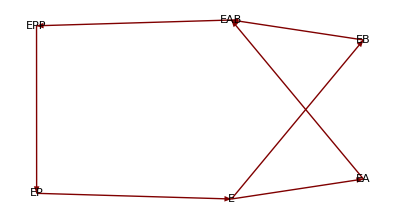
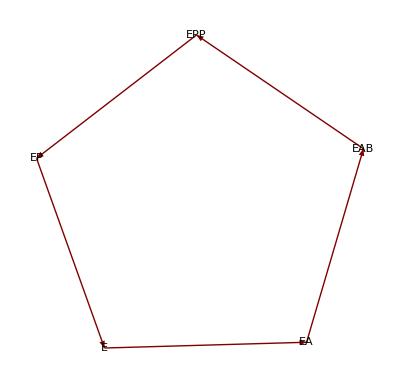
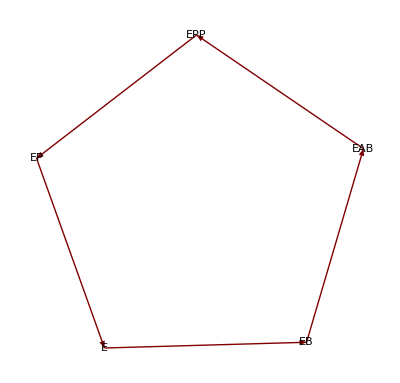

```mathematica
rxn = Cases[iJO["Reactions"],r_reaction/;getID[r]==="ADK1"][[1]]

clelandMechNames={"RandomBinding","OrderedBinding1","OrderedBinding2"}
clelandMech={{"E"->"EA","E"->"EB","EA"->"EAB","EB"->"EAB","EAB"->"EPP","EPP"->"EP","EP"->"E"},{"E"->"EA","EA"->"EAB","EAB"->"EPP","EPP"->"EP","EP"->"E"},{"E"->"EB","EB"->"EAB","EAB"->"EPP","EPP"->"EP","EP"->"E"}};
Table[GraphPlot[clelandMech[[i]],VertexLabeling->True,DirectedEdges->True],{i,1,Length[clelandMech]}]
enzymeModel=Table[constructEnzymeModule[ID->"ADK1",Compartment->"c",Substrates->{m["amp","c"],m["atp","c"]},Products->{m["adp","c"],m["adp","c"]},Mechanism->clelandMech[[i]],ActivationSites->0,InhibitionSites->0],{i,1,Length[clelandMech]}];
```

### Setup King-Altmann Equations

```mathematica
transitionIndex = 5;
reverseZeroSub = {m["adp", "c"] -> 0};
forwardZeroSub = {m["amp", "c"] -> 0, m["atp", "c"] -> 0};
metSatForSub = {m["amp", "c"] -> ∞, m["atp", "c"] -> ∞};
metSatRevSub = { m["adp", "c"] -> ∞};
volumeSub = {parameter["Volume","c"]->1};
KeqName = "ADK1";
KeqVal = 2.3;
```

```mathematica
kaPatterns=Table[unifyRateConstants[keq2k@KingAltmanPatterns[enzymeModel[[i]]]],{i,1,Length[enzymeModel]}];
kaPatterns=Table[anonymize[Simplify[kaPatterns[[i]]]],{i,1,Length[kaPatterns]}];
rndParam=Table[#->RandomReal[]&/@Union@Cases[{unifyRateConstants[kaPatterns[[i]]]},_rateconst|_parameter,∞],{i,1,Length[kaPatterns]}];
allRateConsts = Table[Union[Cases[{kaPatterns},_rateconst,∞]],{i,1,Length[kaPatterns]}];
catalyticRxns=Table[Cases[enzymeModel[[i]]["Reactions"],r_reaction/;StringMatchQ[getID[r],RegularExpression[".*Catalysis.*"]]],{i,1,Length[enzymeModel]}];
haldane=Table[unifyRateConstants[haldaneRelation[KeqName,catalyticRxns[[i]]]],{i,1,Length[enzymeModel]}];
haldaneSub = Join[Quiet[Table[Solve[haldane[[i]] /.{haldane[[i,1]]->  KeqVal},allRateConsts[[i,1]]][[1]],{i,1,(Length[haldane]-1)}],{Solve::ratnz}],Quiet[Table[Solve[haldane[[i]] /.{haldane[[i,1]]->  KeqVal},allRateConsts[[i,3]]][[1]],{i,Length[haldane],Length[haldane]}],{Solve::ratnz}]];(*Kind of a bad hack. Maybe do each individually and join them after*)
rates=Table[enzymeModel[[i]]["Rates"]/.elem_[t]:>elem,{i,1,Length[enzymeModel]}];
absoluteRateForward = Table[(Simplify[keq2k[unifyRateConstants[rates[[i]][[transitionIndex ]]]]/.kaPatterns[[i]]]/.reverseZeroSub/.volumeSub)/.haldaneSub[[i]],{i,1,Length[rates]}];
absoluteRateReverse = Table[(-Simplify[keq2k[unifyRateConstants[rates[[i]][[transitionIndex ]]]]/.kaPatterns[[i]]]/.forwardZeroSub/.volumeSub)/.haldaneSub[[i]],{i,1,Length[rates]}];


(*Each distinct substrate needs it own relative and absolute rate*)
relativeRateForward = Table[absoluteRateForward[[i]]/(Limit[Simplify[keq2k[unifyRateConstants[rates[[i]][[transitionIndex ]]]]/.kaPatterns[[i]]]/.reverseZeroSub/.volumeSub,metSatForSub[[j]]]/.haldaneSub[[i]]),{i,1,Length[rates]},{j,1,Length[metSatForSub]}];
relativeRateReverse = Table[-absoluteRateReverse[[i]]/(Limit[Simplify[keq2k[unifyRateConstants[rates[[i]][[transitionIndex ]]]]/.kaPatterns[[i]]]/.forwardZeroSub/.volumeSub,metSatRevSub[[j]]]/.haldaneSub[[i]]),{i,1,Length[rates]},{j,1,Length[metSatRevSub]}];
finalRateConsts = Table[Union[Cases[{allRateConsts[[i]]/.haldaneSub[[i]]},_rateconst,∞]],{i,1,Length[haldaneSub]}];
rateConstsSub = Table[Thread[finalRateConsts[[i]]-> Table["x["<>ToString[j]<>"]",{j,0,Length[finalRateConsts[[i]]]-1}]],{i,1,Length[finalRateConsts]}];
finalMets = Table[Union[Cases[Flatten[Join[{absoluteRateForward[[i]]},{absoluteRateReverse[[i]]},relativeRateForward[[i]],relativeRateReverse[[i]]]],_metabolite|_parameter,∞]],{i,1,Length[absoluteRateForward]}];
metsSub = Table[Thread[finalMets[[i]]-> Table["d["<>ToString[j]<>"]",{j,0,Length[finalMets[[i]]]-1}]],{i,1,Length[finalMets]}];
```

### Check Equations (Optional)

```mathematica
absoluteRateForwardFinal = Table[absoluteRateForward[[i]]/.rateConstsSub[[i]]/.metsSub[[i]],{i,1,Length[absoluteRateForward]}];
absoluteRateForwardFinalPy=Table[ToPython[absoluteRateForwardFinal[[i]]],{i,1,Length[absoluteRateForwardFinal]}];
absoluteRateForwardFinalPy[[1]]
```

### Export Equations

```mathematica
eqnNameList = {Table[{mechName<>"AbsRateFor1",mechName<>"AbsRateRev1",mechName<>"RelRateFor1",mechName<>"RelRateFor2",mechName<>"RelRateRev1"},{mechName,clelandMechNames}]};
eqnValListPy= {Transpose[{Table[ToPython[absoluteRateForward[[i]]/.rateConstsSub[[i]]/.metsSub[[i]]],{i,1,Length[absoluteRateForward]}],
			Table[ToPython[absoluteRateReverse[[i]]/.rateConstsSub[[i]]/.metsSub[[i]]],{i,1,Length[absoluteRateReverse]}],
			Table[ToPython[relativeRateForward[[i,1]]/.rateConstsSub[[i]]/.metsSub[[i]]],{i,1,Length[relativeRateForward]}],
			Table[ToPython[relativeRateForward[[i,2]]/.rateConstsSub[[i]]/.metsSub[[i]]],{i,1,Length[relativeRateForward]}],
			Table[ToPython[relativeRateReverse[[i,1]]/.rateConstsSub[[i]]/.metsSub[[i]]],{i,1,Length[relativeRateReverse]}]}]};
eqnValList= Transpose[{Table[absoluteRateForward[[i]],{i,1,Length[absoluteRateForward]}],
			Table[absoluteRateReverse[[i]],{i,1,Length[absoluteRateReverse]}],
			Table[relativeRateForward[[i,1]],{i,1,Length[relativeRateForward]}],
			Table[relativeRateForward[[i,2]],{i,1,Length[relativeRateForward]}],
			Table[relativeRateReverse[[i,1]],{i,1,Length[relativeRateReverse]}]}];
eqnList=Join[eqnNameList,eqnValListPy];
parallelOutputPath=Table[outputPath<>mechName<>"/",{mechName,clelandMechNames}];
fileList=Table[parallelOutputPath[[i]]<>eqnname<>".txt",{i,1,Length[eqnList[[1]]]},{eqnname,eqnList[[1,i]]}];
mkDirCmdParallel = Table["!mkdir "<>parallelPath<> " 2>&1",{parallelPath,parallelOutputPath}];
Table[Import[cmd,"Text"],{cmd,mkDirCmdParallel}];
fileListSub=Table[fileList[[i,j]]->eqnValList[[i,j]],{i,1,Length[fileList]},{j,1,Length[fileList[[1]]]}];
Table[Export[fileList[[i,j]], eqnList[[2,i,j]]],{i,1,Length[eqnList[[2]]]},{j,1,Length[eqnList[[2,1]]]}];
```

## Simulate Data (in Parallel)

### Setting Parameters to Generate Data

```mathematica
extraData = {pHVal,tempVal,fileFlag};
extraDataNames={"pH","temp","fileFlag","vRel"};
totalVarListNames = Table[Join[getID/@metsSub[[i,All,1]],extraDataNames],{i,1,Length[metsSub]}];
totalVarList = Table[Join[metsSub[[i,All,1]],extraData],{i,1,Length[metsSub]}];
KmList={KmAdp,KmAtp,KmAmp,n}={0.000105,0.000046,0.000044,1};
```

### Generating Data

```mathematica
vListData={};
Do[{vList={};
ADP  (All concentrations in Mol/L);
extraSub = {pHVal-> 7.4,tempVal-> 40,fileFlag-> fileList[[index,5]]};
metsSubData = {m["amp","c"]-> 0,m["atp","c"]-> 0,parameter["Etot"]-> 1};
varMet = m["adp","c"];
kmData = KmAdp;
varMetIndex = 1;

{minRange, maxRange,step}={(Log10[kmData]-1),(Log10[kmData]+1),.2};
dataRange = Table[totalVarList[[index]]/.extraSub/.metsSubData/.varMet->10^i,{i,minRange,maxRange,step}];

vRelVal= #^n/(kmData^n+#^n)&/@dataRange[[All,varMetIndex]];
vList = Append[vList, Table[Join[dataRange[[i]],{vRelVal[[i]]}],{i,1,Length[dataRange]}]];
ATP  (All concentrations in Mol/L);
extraSub = {pHVal-> 7.4,tempVal-> 40,fileFlag-> fileList[[index,4]]};
metsSubData = {m["amp","c"]-> 0.001,m["adp","c"]-> 0,parameter["Etot"]-> 1};
varMet = m["atp","c"];
kmData = KmAtp;
varMetIndex = 3;

{minRange, maxRange,step}={(Log10[kmData]-1),(Log10[kmData]+1),.2};
dataRange = Table[totalVarList[[index]]/.extraSub/.metsSubData/.varMet->10^i,{i,minRange,maxRange,step}];

vRelVal= #^n/(kmData^n+#^n)&/@dataRange[[All,varMetIndex]];
vList = Append[vList,Table[Join[dataRange[[i]],{vRelVal[[i]]}],{i,1,Length[dataRange]}]];
AMP  (All concentrations in Mol/L);
extraSub = {pHVal-> 7.4,tempVal-> 40,fileFlag-> fileList[[index,3]]};
metsSubData = {m["atp","c"]-> 0.001,m["adp","c"]-> 0,parameter["Etot"]-> 1};
varMet = m["amp","c"];
kmData = KmAmp;
varMetIndex = 2;

{minRange, maxRange,step}={(Log10[kmData]-1),(Log10[kmData]+1),.2};
dataRange = Table[totalVarList[[index]]/.extraSub/.metsSubData/.varMet->10^i,{i,minRange,maxRange,step}];

vRelVal= #^n/(kmData^n+#^n)&/@dataRange[[All,varMetIndex]];
vList = Append[vList,Table[Join[dataRange[[i]],{vRelVal[[i]]}],{i,1,Length[dataRange]}]];

kcat[ADP] value (All concentrations in Mol/L);
extraSub = {pHVal-> 7.4,tempVal-> 40,fileFlag-> fileList[[index,2]]};
metsSubData = {m["atp","c"]-> 0,m["amp","c"]-> 0,parameter["Etot"]-> 1};
varMet = m["adp","c"];
kcatRev=319;
kmData = KmAdp;
varMetIndex = 1;

dataPoint = totalVarList[[index]]/.extraSub/.metsSubData/.varMet->0.01;
vAbsVal= #^n/(kmData^n+#^n)*kcatRev*parameter["Etot"]/.metsSubData&/@{dataPoint[[varMetIndex]]};
(*vList = Append[vList,{Join[dataPoint,{vAbsVal}]}];*)
vList =Append[vList,Table[Join[dataPoint,vAbsVal],{i,1,10}]];

kcat[ATP,AMP] value (All concentrations in Mol/L);
extraSub = {pHVal-> 7.4,tempVal-> 40,fileFlag-> fileList[[index,1]]};
metsSubData = {m["adp","c"]-> 0,parameter["Etot"]-> 1};
varMet = {m["amp","c"]-> 0.01,m["atp","c"]->0.01};
kcatFor =1296;
kmData = {KmAmp,KmAtp};
dataPoint = {totalVarList[[index]]/.extraSub/.metsSubData/.varMet};

vAbsVal= (#1[[3]] #1[[2]])^n/((kmData[[1]] #1[[3]])^n+(kmData[[2]] #1[[2]])^n+(#1[[3]] #1[[2]])^n)*kcatFor*parameter["Etot"]/.metsSubData&/@dataPoint;

(*vList = Append[vList,{Join[Flatten[dataPoint,1],vAbsVal]}];*)
vList = Append[vList,Table[Join[Flatten[dataPoint,1],vAbsVal],{i,1,10}]];

vListData = Join[vListData,{Flatten[vList,1]}];},{index,1,Length[clelandMech]}]
```

### Writing to a .txt file

```mathematica
(*labels = {{"v","M_adp_c","M_atp_c","M_amp_c","pH","Temp","Etot","RelFlag"}}*)
header = Table[{totalVarListNames[[i]]},{i,1,Length[totalVarListNames]}];
vList=Table[Join[header[[i]],vListData[[i]]],{i,1,Length[header]}];
dataPath =Table[parallelPath<>"ADK1.dat",{parallelPath,parallelOutputPath}];
Table[Export[dataPath[[i]],vList[[i]],"Table"],{i,1,Length[dataPath]}];
```

```mathematica
(*Optional*)
Table[FilePrint[dataFile],{dataFile,dataPath}]
```

## Run the Particle Swarm Optimization (in Parallel)

### Setting the Python Script Parameters

```mathematica
psoParameters=Table[{(*Problem Scaling*)
				numSigFig=4, (*rounding of the objective function (make lower to allow more equivalent parameters sets)*)
				gridPopSize=20,(*Population Size for the grid*)
				finalPopSize=100,(*Population Size for the final fitting*)
				gridGenerations=10,(*Generation Termination*)
				finalGenerations=4000,(*Generation Termination*)
				topWorkingSize=50,(*Number of parameter sets taken from grid sampling based on best_fit*)
				maxFinalSets=1,(*Number of top parameter sets used from the grid results, sorted for highest standard deviation from the topWorkingSize population*)
				finalNumTrial=90,(*Number of trials for each parameter set in the final fitting*)
				SimilarityLimit=0.01,(*Tolerance for parameter set similarity (Log scale)*)
				numCpus=14,(*Number of processor cores*)

				(*PSO Behavior*)
				(*Warning: These drastically change the computation time*)
				minDiversityValue=0.0000001,(*Should be very small*)
				(*minDiversityVal=0.0001,*)
				minNeighVal=10,(*minimum neighborhood size, default size is 3*)
				maxNeighVal=10,(*maximum neighborhood size*)
				gridSize=1,(*Centered around the default arguments (1.0,2.1,2.1) and varied in logirithmic proportional to the grid size (e.g.w/grid_size=5,default arguments are at grid point 3 and the step size is 1.0*10**(1/3) for intertia and 2.1*10**(1/3) for cognitive and social rates)*)

				(*Variable Info*)
				lowerBound=-2.0,(*Lower parameter range (Log scale)*)
				upperBound=9.0,(*Upper parameter range (Log scale)*)
				numFuncVar=Length[finalRateConsts[[i]]],

				(*Data Info*)
				(*Note: dataPath -> data_file_name*)
				(*Note: vRel functions pH and temp are in expected positions*)
				dataFileName=dataPath[[i]],
				psoStatsFileName=parallelOutputPath[[i]]<>"pso_stats.tmp",
				individualsFileName=parallelOutputPath[[i]]<>"individuals.tmp",
				trialSummaryFileName=parallelOutputPath[[i]]<>"summary.txt",
				resultsFileName = parallelOutputPath[[i]]<>"results.txt"},{i,1,Length[clelandMechNames]}];
(*fileList -> filesWithFunctions*)
Do[psoParameters[[i]]=Join[psoParameters[[i]],fileList[[i]]],{i,1,Length[fileList]}];
parameterPath =Table[parallelPath<>"psoParameters.txt",{parallelPath,parallelOutputPath}];
Table[Export[parameterPath[[i]],psoParameters[[i]],"Table"],{i,1,Length[psoParameters]}];
```

### Running the Script from a shell

```mathematica
psoCmd=Table["!python "<>psoScriptPath<>" "<>paramPath<>" 2>&1",{paramPath,parameterPath}]
```

```mathematica
(*This might take a while depending on the psoParameters*)
Table[Import[run,"Text"],{run,psoCmd}](*Not Sure if this is how we want to do this*)
```

# Development Section

## Old Stuff

```mathematica
(*Pull in parameters and check fit and enzyme stats*)

(*paramFit=Import[resultsFileName]
paramFitProcessed=10^ToExpression[StringSplit[StringReplace[paramFit,{"["->"","]"->"","e"->"*^"}],RegularExpression[","]]]
paramFitSub=Thread[rateConstsSub[[All,1]]->paramFitProcessed]

"[-3.9051536277572518, -1.3993180219197792, -2.9327693848904262, -0.043968254849804135, 4.3088823495289876, -1.4851761954658167, 2.8295567758387308, 2.2228170894589185, -2.4914110753760959, -0.1111952634925482, 3.1902595709939594, 9.0, 5.1250221734209287]	"

{0.000124407,0.0398733,0.00116743,0.903716,20364.9,0.0327208,675.393,167.039,0.00322544,0.774114,1549.74,1.*10^9,133359.}

{MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Bind(EA->EAB)",True]->0.000124407,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Bind(EB->EAB)",False]->0.0398733,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Bind(EB->EAB)",True]->0.00116743,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Bind(E->EA)",False]->0.903716,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Bind(E->EA)",True]->20364.9,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Bind(E->EB)",False]->0.0327208,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Bind(E->EB)",True]->675.393,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Release(EP->E)",False]->167.039,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Release(EP->E)",True]->0.00322544,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Release(EPP->EP)",False]->0.774114,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Release(EPP->EP)",True]->1549.74,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Transition(EAB->EPP)",False]->1.*10^9,MASStoolbox`MASS`rateconst["ADK1_R_Catalysis_Transition(EAB->EPP)",True]->133359.}

relRateRevFit=relativeRateReverse[[1]]/.paramFitSub

(9.73622*10^9 MASStoolbox`MASS`metabolite["adp","c"])/(1.02353*10^6+9.73622*10^9 MASStoolbox`MASS`metabolite["adp","c"])

extraSub={pHVal->7.4,tempVal->40,fileFlag->fileList[[3]]};
metsSubData={m["amp","c"]->0,m["atp","c"]->0,parameter["Etot"]->1};
varMet=m["adp","c"];
kmData=KmAdp;
varMetIndex=1;

{minRange,maxRange,step}={(Log10[kmData]-1),(Log10[kmData]+1),.2};
dataRange=Table[totalVarList/.extraSub/.metsSubData/.varMet->10^i,{i,minRange,maxRange,step}];

vRelVal=#^n/(kmData^n+#^n)&/@dataRange[[All,varMetIndex]]

{0.0909091,0.136807,0.20076,0.284747,0.386863,0.5,0.613137,0.715253,0.79924,0.863193,0.909091}

vRelFit=relRateRevFit/.#&/@Table[varMet->dataRange[[i,1]],{i,1,Length[dataRange]}]

{0.0908096,0.136665,0.200567,0.284502,0.386578,0.499699,0.612851,0.715007,0.799047,0.863051,0.908991}

vRelSSD=Total[Table[(vRelVal[[i]]-vRelFit[[i]])^2,{i,1,Length[vRelVal]}]]

5.09075*10^-7*)
```

```mathematica
(*Calculate the PCA of the parameters*)
```

```mathematica
(*Calculate Function Derivatives*)
(*Needs to be updated to use Keq's instead of k-*)(*Also, not being used by anything*)

gradient={};
Do[gradient=Append[gradient,Table[D[eqnList[[3,eqn]],rateConstsSub[[var,1]]],{var,Length[rateConstsSub]}]],{eqn,Length[eqnList[[3]]]}];(*Create a list of partial derivatives for each rate equation*)
gradientPy=Table[ToPython[gradient[[eqn,pDeriv]]/.rateConstsSub/.metsSub],{eqn,Length[gradient]},{pDeriv,Length[gradient[[1]]]}];(*Switch the p. derivative equations to a python format*)
gradientDir=Table[outputPath<>"D_Functions/"<>eqnNameList[[name]]<>"/",{name,Length[eqnNameList]}];(*Create a directory list for equation output*)
mkParentDirCmd="!mkdir "<>outputPath<>"D_Functions/ 2>&1";(*Make a folder to store all of the rate equation folders*)
Import[mkParentDirCmd,"Text"];
mkSubDirCmd = Table["!mkdir "<>gradientDir[[path]]<> " 2>&1",{path,Length[gradientDir]}];(*Make folders for each rate equation to store the partial derivatives*)
Do[Import[mkSubDirCmd[[dir]],"Text"],{dir,Length[mkSubDirCmd]}];
gradFileList=Table[gradientDir[[path]]<>"PartialDer"<>ToString[varNum]<>".txt",{path,Length[gradientDir]},{varNum,Length[rateConstsSub[[All,1]]]}];(*Create the file names for each partial derivative*)
Do[Export[gradFileList[[eqn,pDeriv]],gradientPy[[eqn,pDeriv]]],{eqn,Length[gradFileList]},{pDeriv,Length[gradFileList[[1]]]}];(*Export the equations*)
```

### Construct Enzyme Module

```mathematica
clelandMech={"E"->"EA","E"->"EB","EA"->"EAB","EB"->"EAB","EAB"->"EPP","EPP"->"EP","EP"->"E"};
GraphPlot[clelandMech,VertexLabeling->True,DirectedEdges->True]
enzymeModel=constructEnzymeModule[ID->"ADK1",Compartment->"c",Substrates->{m["amp","c"],m["atp","c"]},Products->{m["adp","c"],m["adp","c"]},Mechanism->clelandMech,ActivationSites->0,InhibitionSites->0];
```

## Sandbox (For Development and Debugging)

```mathematica
(*Developent*)
(*Length[enzymeModel["Reactions"]]
TableForm[S[enzymeModel]]
Total[S[enzymeModel]]
Length[Transpose[S[enzymeModel]]]
Length[Union[Cases[getReactions[enzymeModel],_metabolite|_enzyme,∞]]]
TableForm[{Transpose[S[enzymeModel]],model2reactionList[enzymeModel]}];*)
```

7

-1 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 1 | 0
0 | 1 | 0 | -1 | 0 | 0 | 0
1 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 1
0 | 0 | 1 | 0 | 0 | 1 | 0
0 | -1 | 0 | 0 | -1 | 0 | 0
-1 | 0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | -1

{-1,-1,1,-1,-1,1,0}

7

9

```mathematica
(*catalyticRxnIndex=*)

(*numberProducts=Table[Length[getProducts[allReactions[[eqn]]]],{eqn,Length[enzymeModel["Reactions"]]}]
numberSubstrates=Table[Length[getSubstrates[allReactions[[eqn]]]],{eqn,Length[enzymeModel["Reactions"]]}]
numberSubstrates-numberProducts*)
```

```mathematica
(*tmp1=enzymeModel["Reactions"][[1]]
FullForm[tmp1]*)
```

```mathematica
(*sumReactionStoich*)
```

```mathematica
(*enzymeModel["ReverseRateConstants"]*)
```

```mathematica
(*transitionIndex={};
forwardBindingIndex={};
reverseBindingIndex={};
allReactions=enzymeModel["Reactions"];
sumReactionStoich=Table[Total[getSignedStoich[allReactions[[eqn]]]],{eqn,Length[allReactions]}]
Table[If[sumReactionStoich[[eqn]] ==0,transitionIndex=Append[transitionIndex,eqn]],{eqn,Length[sumReactionStoich]}];(*Extract the transition step(s)*)
Table[If[sumReactionStoich[[eqn]] <0,forwardBindingIndex=Append[forwardBindingIndex,eqn]],{eqn,Length[sumReactionStoich]}];(*Extract the binding step(s) if the reaction is proceeding forward*)
Table[If[sumReactionStoich[[eqn]] >0,reverseBindingIndex=Append[reverseBindingIndex,eqn]],{eqn,Length[sumReactionStoich]}];(*Extract the binding step(s) if the reaction is proceeding in reverse*)*)
```

```mathematica
(*Development: Extract Catalytic Steps*)(*Broken*)
(*tmp=ToExpression[StringCases[ToString[FullForm[allRateConsts]],RegularExpression["rateconst\\[\"[^_]+_[^_]_Catalysis_Transition\\([^)]+\\)\", False\\]"]][[1]]];*)
```

```mathematica
(*allReactions*)
```

```mathematica
forwardRateConsts=enzymeModel["ForwardRateConstants"]
reverseRateConsts=enzymeModel["ReverseRateConstants"]
forwardDissociationConsts=Table[{forwardRateConsts[[forwardBindingIndex[[index]]]],reverseRateConsts[[forwardBindingIndex[[index]]]]},{index,Length[forwardBindingIndex]}]
reverseDissociationConsts=Table[{reverseRateConsts[[reverseBindingIndex[[index]]]],forwardRateConsts[[reverseBindingIndex[[index]]]]},{index,Length[reverseBindingIndex]}]
linearConstraintsForFitting=Join[forwardDissociationConsts,reverseDissociationConsts]
linearConstraintsForFittingPy=Table[ToString[linearConstraintsForFitting[[i]]/.rateConstsSub],{i,Length[linearConstraintsForFitting]}]
(*Export[outputPath<>"linearConstraints.txt",linearConstraintsForFittingPy,"Table"];*)
```

{k_ADK11^⟶,k_ADK12^⟶,k_ADK13^⟶,k_ADK14^⟶,k_ADK15^⟶,k_ADK16^⟶,k_ADK17^⟶}

{k_ADK11^⟵,k_ADK12^⟵,k_ADK13^⟵,k_ADK14^⟵,k_ADK15^⟵,k_ADK16^⟵,k_ADK17^⟵}

{{k_ADK11^⟶,k_ADK11^⟵},{k_ADK12^⟶,k_ADK12^⟵},{k_ADK14^⟶,k_ADK14^⟵},{k_ADK15^⟶,k_ADK15^⟵}}

{{k_ADK13^⟵,k_ADK13^⟶},{k_ADK16^⟵,k_ADK16^⟶}}

{{k_ADK11^⟶,k_ADK11^⟵},{k_ADK12^⟶,k_ADK12^⟵},{k_ADK14^⟶,k_ADK14^⟵},{k_ADK15^⟶,k_ADK15^⟵},{k_ADK13^⟵,k_ADK13^⟶},{k_ADK16^⟵,k_ADK16^⟶}}

{{x[1], x[0]},{x[3], x[2]},{x[7], x[6]},{x[9], x[8]},{x[4], x[5]},{x[10], x[11]}}

```mathematica
TableForm[linearConstraintsForFitting]/.rateConstsSub
```

x[1] | x[0]
x[3] | x[2]
x[7] | x[6]
x[9] | x[8]
x[4] | x[5]
x[10] | x[11]

## Notes

```mathematica
(*
1. Sig fig in variables (DONE)
2. ea create and delete (DONE)
3. Run longer and smaller grid (DONE)
4. Make notebook multi-mechanism (IN PROGRESS)
5. Change pH to [H] by [H] = 10^-pH (DONE)
6. Use pH and Arrhenius and ordered as test cases for multi-mechanism
 *)
```